```mathematica
matrix
```

matrix

```mathematica
mat = {{1/2, 1/2,1/6,0}, {1/4,1/2,1/6,0}, {1/4,0,1/2,1/2}, {0,0,1/6,1/2}};
mat2 = {{1},{0},{0},{0}};
m1=mat//MatrixForm
m2 = mat2//MatrixForm
```

(1/2 | 1/2 | 1/6 | 0
1/4 | 1/2 | 1/6 | 0
1/4 | 0 | 1/2 | 1/2
0 | 0 | 1/6 | 1/2)

(1
0
0
0)

```mathematica
mat3 = N[MatrixPower[mat,n]];
N[MatrixPower[mat,100]]//MatrixForm
N[MatrixPower[mat,100]].mat2//MatrixForm
```

(0.363636 | 0.363636 | 0.363636 | 0.363636
0.272727 | 0.272727 | 0.272727 | 0.272727
0.272727 | 0.272727 | 0.272727 | 0.272727
0.0909091 | 0.0909091 | 0.0909091 | 0.0909091)

(0.363636
0.272727
0.272727
0.0909091)

```mathematica
(*Q3.1 - 1*)
```

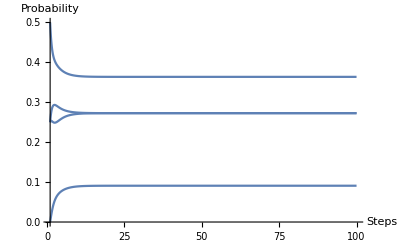

```mathematica
mat3.mat2// MatrixForm;
Plot[mat3.mat2, {n, 1, 100},AxesLabel->{Steps,Probability}]
```

```mathematica
λ1 = {{λ,0,0,0},{0,λ,0,0},{0,0,λ,0},{0,0,0,λ} };
λ1 //MatrixForm
eige = mat - λ1 
Det[eige]
```

(λ | 0 | 0 | 0
0 | λ | 0 | 0
0 | 0 | λ | 0
0 | 0 | 0 | λ)

{{1/2-λ,1/2,1/6,0},{1/4,1/2-λ,1/6,0},{1/4,0,1/2-λ,1/2},{0,0,1/6,1/2-λ}}

(36-468 λ+2160 λ^2-3456 λ^3+1728 λ^4)/1728

```mathematica
Factor[(36-468 λ+2160 λ^2-3456 λ^3+1728 λ^4)/1728]
```

1/48 (-1+λ) (-1+12 λ-48 λ^2+48 λ^3)

```mathematica
FullSimplify[1/48 (-1+λ) (-1+12 λ-48 λ^2+48 λ^3)]
```

1/48 (-1+λ) (-1+12 (1-2 λ)^2 λ)

```mathematica
N[Solve[Det[eige]==0, λ]]
```

{{λ→1.},{λ→0.675604},{λ→0.162198-0.0672931 ⅈ},{λ→0.162198+0.0672931 ⅈ}}

```mathematica
(*3.1.4*)

mat4 = {{1/2, 1/2, 1/6,0,0}, {1/4,1/2,1/6,0,0}, {1/4, 0,1/2,1/4,0}, {0,0,1/6,1/2,0},{0,0,0,1/4,1}};
mat4//MatrixForm
```

(1/2 | 1/2 | 1/6 | 0 | 0
1/4 | 1/2 | 1/6 | 0 | 0
1/4 | 0 | 1/2 | 1/4 | 0
0 | 0 | 1/6 | 1/2 | 0
0 | 0 | 0 | 1/4 | 1)

```mathematica
m4 = {{1},{0},{0},{0},{0}};
Ma1=N[MatrixPower[mat4,n]];
```

(0.00550719 | 0.00575259 | 0.00479192 | 0.00250273 | 0.
0.00410039 | 0.0042831 | 0.00356783 | 0.00186341 | 0.
0.00351561 | 0.00367227 | 0.00305901 | 0.00159766 | 0.
0.00122409 | 0.00127864 | 0.00106511 | 0.000556284 | 0.
0.985653 | 0.985013 | 0.987516 | 0.99348 | 1.)

(0.00550719
0.00410039
0.00351561
0.00122409
0.985653)

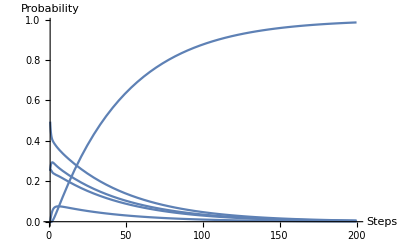

```mathematica
N[MatrixPower[mat4,200]]//MatrixForm
N[MatrixPower[mat4,200]].m4//MatrixForm
Plot[Ma1.m4, {n, 1, 200},AxesLabel->{Steps,Probability}]
```

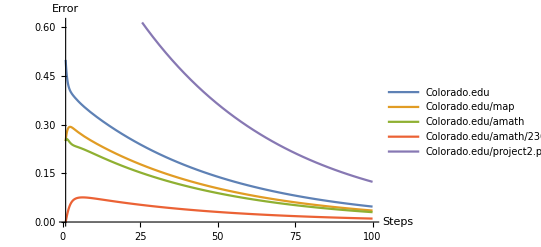

```mathematica
(*Q3.1.5*)
v1 = {{0},{0},{0},{0},{1}};
Error1 = Abs[v1 - Ma1.m4];
Plot[Error1,{n,1,100}, AxesLabel->{Steps,Error},PlotLegends-> LineLegend[{"Colorado.edu", "Colorado.edu/map", "Colorado.edu/amath", "Colorado.edu/amath/2360", "Colorado.edu/project2.pdf"}]]
```